## Analysis of SimTree output

```mathematica
demeCount=3;
```

```mathematica
clipStartTime=-10;
```

```mathematica
clipEndTime=100;
```

```mathematica
SetDirectory[$HomeDirectory<>"/Documents/current-projects/SimTree/output/saved-20-good"]
```

/Users/bedfordt/Documents/current-projects/SimTree/output/saved-20-good

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree/source

## Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Setup

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

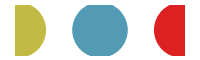

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},AspectRatio->0.3,ImageSize->200]
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors];
```

```mathematica
trunkColors={GrayLevel[0.3],RGBColor[0.857,0.131,0.132]};
```

```mathematica
trunkColorRules=MapIndexed[#2[[1]]-1->#1&,trunkColors];
```

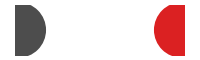

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,trunkColors]},AspectRatio->0.3,ImageSize->200]
```

```mathematica
dist[coord_]:=EuclideanDistance[{0,0},coord]
```

## Assumptions

### R0

5 day recovery

```mathematica
0.2*1.5
```

0.3

### Mutation

```mathematica
0.00014*365/0.005
```

10.22

```mathematica
0.01*365/0.005
```

730.

Let’s say there are 10 sites that function to move the virus in phenotype space

```mathematica
5*0.005*(1/365)
```

0.0000684932

```mathematica
10*0.005*(1/365)
```

0.000136986

Mutations per day

```mathematica
0.25*1.5
```

0.375

```mathematica
N[5*2*10^-5]
```

0.0001

```mathematica
0.2*1.5
```

0.3

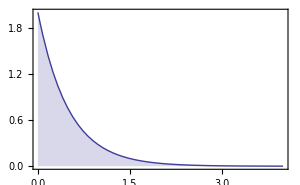

```mathematica
Plot[PDF[ExponentialDistribution[2],x],{x,0,4},ImageSize->300,Filling->Axis]
```

```mathematica
CDF[ExponentialDistribution[2.],2]
```

0.981684

### Cross-immunity

The antigenic map is on a Log2 scale.

Average distance between clusters is 4.5 units.

Rough cross-immunity between clusters is 0.65 to 0.80.

4.5 units = 0.3 risk of infection

```mathematica
4.5*0.067
```

0.3015

```mathematica
7*0.067
```

0.469

```mathematica
TableForm[N[Table[x*0.067,{x,0,6}]],TableHeadings->{Range[0,6]}]
```

0 | 0.
1 | 0.067
2 | 0.134
3 | 0.201
4 | 0.268
5 | 0.335
6 | 0.402

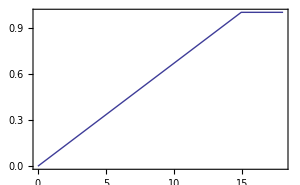

```mathematica
Plot[Clip[x*0.067],{x,0,18},ImageSize->300]
```

### Contact patterns

## World-wide SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

20.

```mathematica
popSize=data[[1,3]]
```

1499980

### Analysis window

```mathematica
data=Select[data,(#[[1]]>clipStartTime&&#[[1]]<clipEndTime&)];
```

### Prevalence

```mathematica
prev=data[[All,{1,5}]];
```

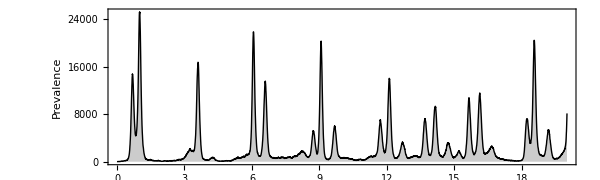

```mathematica
prevfig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]
```

### Incidence

```mathematica
inc=data[[All,{1,7}]];
```

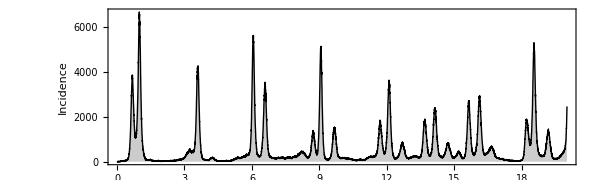

```mathematica
incfig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Incidence"},ImagePadding->{{40,10},{15,5}}]
```

Mean prevelance

```mathematica
N[Mean[prev[[All,2]]]]
```

2388.27

```mathematica
N[Mean[prev[[All,2]]]/popSize]
```

0.0015922

Mean incidence per year

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

219030.

```mathematica
N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.146022

Flu incidence is 10% per year and prevalence is 0.14%.

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

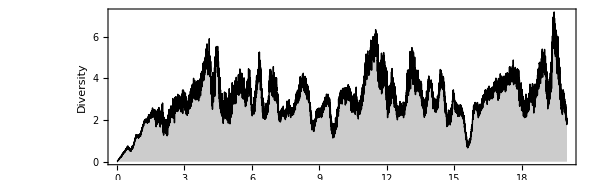

```mathematica
divfig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Diversity"},ImagePadding->{{40,10},{15,5}}]
```

### Combined

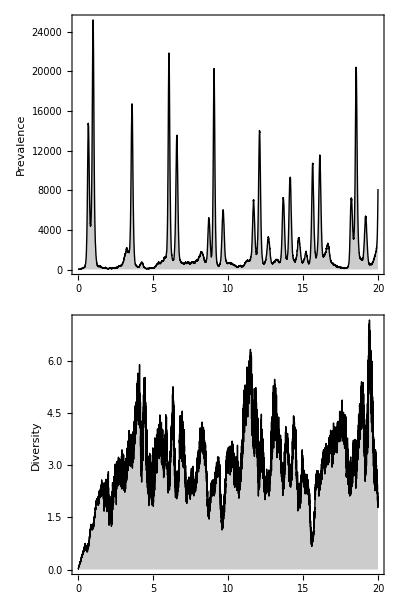

```mathematica
fig=Grid[{{prevfig},{divfig}}]
```

```mathematica
Export["timeseries.pdf",fig,"PDF"]
```

timeseries.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

20.

### Analysis window

```mathematica
data=Select[data,(#[[1]]>clipStartTime&&#[[1]]<clipEndTime&)];
```

### Prevalence

```mathematica
Table[i,{i,10,10+(demeCount-1)*5,5}]
```

{10,15,20}

```mathematica
prevList=Table[data[[All,{1,i}]],{i,10,10+(demeCount-1)*5,5}];
```

```mathematica
max=Max[Map[Max,prevList]]
```

22534

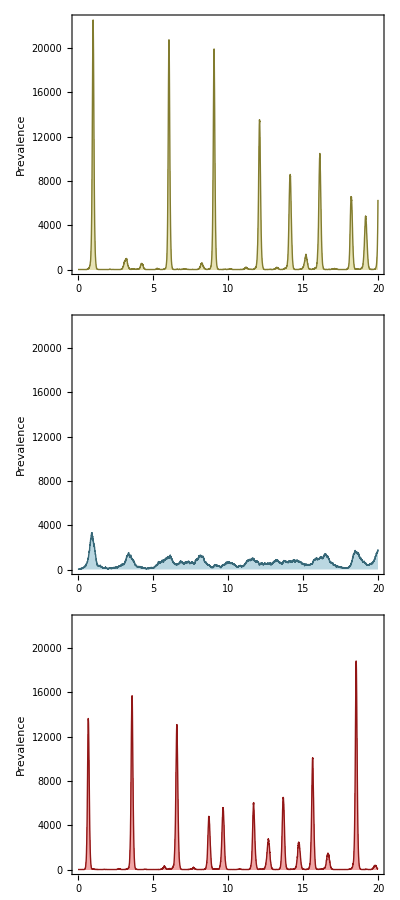

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],PlotRange->{0,max},AspectRatio->0.15,ImageSize->700,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Opacity[0.4,spatialColors[[i]]]],FrameLabel->{"","Prevalence"},ImagePadding->{{50,10},{15,5}}]},{i,demeCount}]]
```

```mathematica
Export["timeseriesSpatial.pdf",fig,"PDF"]
```

timeseriesSpatial.pdf

### Incidence

```mathematica
incList=Table[data[[All,i]],{i,12,12+(demeCount-1)*5,5}];
```

```mathematica
TableForm[N[Map[Total[#]/(endTime-startTime)&,incList]],TableHeadings->{Range[demeCount]}]
```

1 | 82774.8
2 | 57245.4
3 | 79038.9

## Tips

```mathematica
tipScale=0.001;
```

```mathematica
tipData=Import["out.tips","CSV"];
```

```mathematica
Length[tipData]
```

30153

```mathematica
traitHeader=tipData[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[7]}]
```

1 | name
2 | year
3 | trunk
4 | location
5 | layout
6 | ag1
7 | ag1

```mathematica
tipData=Drop[tipData,1];
```

```mathematica
name=1;year=2;trunk=3;loc=4;layout=5;ag1=6;ag2=7;
```

### Analysis window

```mathematica
tipData=Select[tipData,(#[[year]]>clipStartTime&&#[[year]]<clipEndTime&)];
```

### Graphics settings

```mathematica
frameWindow=1.0;
```

```mathematica
plotRange={{Floor[Min[tipData[[All,ag1]]],frameWindow],Ceiling[Max[tipData[[All,ag1]]],frameWindow]},{Floor[Min[tipData[[All,ag2]]],frameWindow],Ceiling[Max[tipData[[All,ag2]]],frameWindow]}}
```

{{-2.,25.},{-35.,4.}}

```mathematica
aspectRatio=Max[Apply[EuclideanDistance,plotRange[[2]]]/Apply[EuclideanDistance,plotRange[[1]]],0.15]
```

1.44444

```mathematica
imageSize=If[aspectRatio>1,600/aspectRatio,600]
```

415.385

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-100,100,frameWindow}],{2},{2}];
```

### Year vs AG1

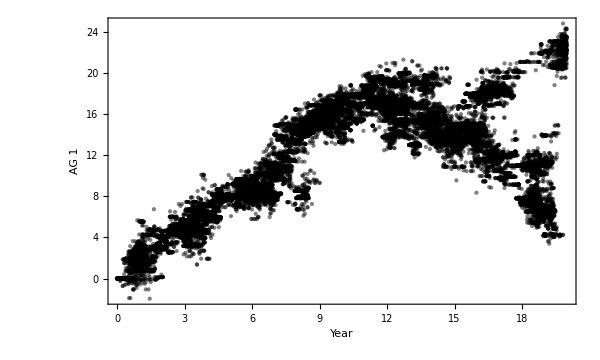

```mathematica
fig=ListPlot[tipData[[All,{year,ag1}]],AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1.pdf",fig,"PDF"]
```

tipsYearAG1.pdf

### Year vs AG2

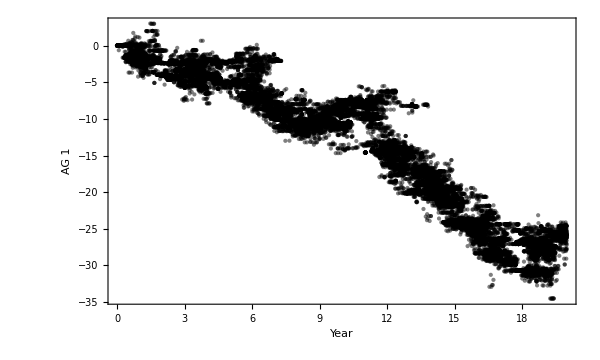

```mathematica
fig=ListPlot[tipData[[All,{year,ag2}]],AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG2.pdf",fig,"PDF"]
```

tipsYearAG2.pdf

### AG1 vs AG2

```mathematica
tallies=Tally[tipData[[All,{ag1,ag2}]]];
```

```mathematica
points=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,tallies];
```

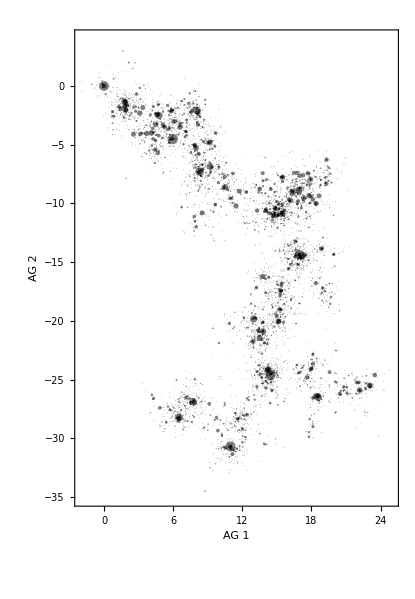

```mathematica
fig=Graphics[{Opacity[0.5],points},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["tipsAG1AG2.pdf",fig,"PDF"]
```

tipsAG1AG2.pdf

### Map

Found average distance between two points of the same strain as 1.6 units

1.6 units is 1.6 * 0.067 = 0.11

```mathematica
spread=0.3;
```

```mathematica
test=Table[RandomVariate[NormalDistribution[0,spread],2],{100}];
```

```mathematica
Mean[Flatten[Table[EuclideanDistance[test[[i]],test[[j]]],{i,Length[test]},{j,i+1,Length[test]}]]]
```

0.512772

```mathematica
jitter=Flatten[Map[Table[#[[1]]+RandomVariate[NormalDistribution[0,spread],2],{Round[0.1*#[[2]]]}]&,tallies],1];
```

```mathematica
Length[jitter]
```

2159

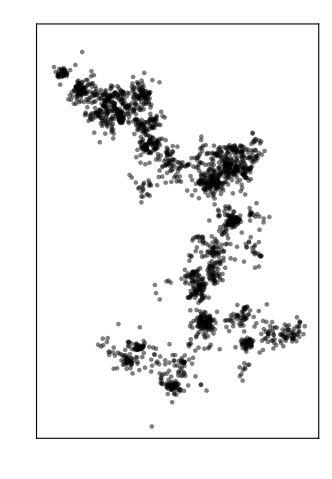

```mathematica
fig=ListPlot[jitter,AspectRatio->aspectRatio,PlotRange->plotRange,PlotStyle->Directive[PointSize[0.01],Black,Opacity[0.5]],GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->GrayLevel[0.9],Frame->True,ImageSize->imageSize*0.8,FrameTicks->None]
```

```mathematica
Export["tipsMap.pdf",fig,"PDF"]
```

tipsMap.pdf

### Distance from origin

```mathematica
list=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

AG change per year

```mathematica
(Max[list[[All,2]]]-Min[list[[All,2]]])/(endTime-startTime)
```

1.91048

Want 1.2 units = 0.08 distance per year

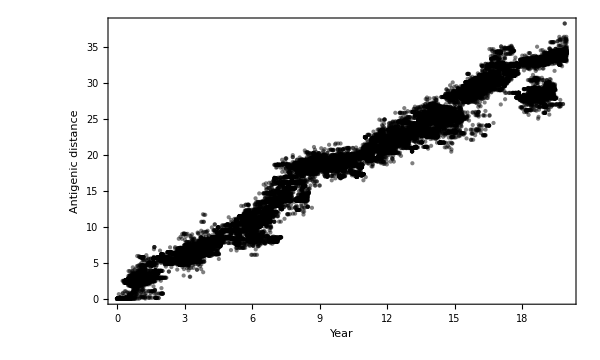

```mathematica
fig=ListPlot[list,AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","Antigenic distance"}]
```

```mathematica
Export["tipsYearDistance.pdf",fig,"PDF"]
```

tipsYearDistance.pdf

```mathematica
list=Map[{#[[1]],#[[2]],dist[#[[{3,4}]]]}&,tipData[[All,{year,loc,ag1,ag2}]]];
```

```mathematica
window=0.5;
```

```mathematica
meanlists=Table[Table[{i+window/2,Mean[Select[list,(#[[2]]==j&&#[[1]]>i&&#[[1]]<i+window&)][[All,3]]]},{i,Floor[startTime],Ceiling[endTime]-window,window}],{j,0,demeCount-1}];
```

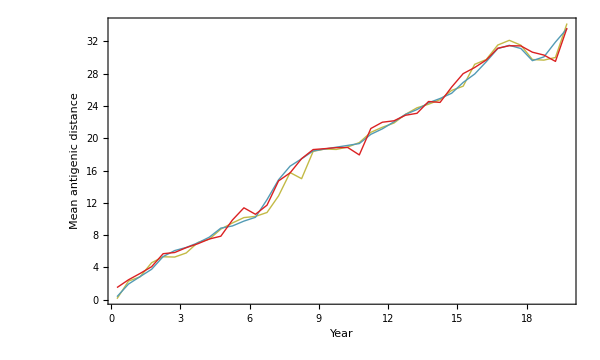

```mathematica
fig=ListLinePlot[meanlists,AspectRatio->0.6,PlotRange->All,PlotStyle->spatialColors,FrameLabel->{"Year","Mean antigenic distance"},ImageSize->600]
```

```mathematica
Export["tipsYearDistanceMean.pdf",fig,"PDF"]
```

tipsYearDistanceMean.pdf

### Loess spline

```mathematica
data=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
fit[x_]:=LoessFit[x,data,0.2,1]
```

```mathematica
startTime=Min[data[[All,1]]]
```

0.

```mathematica
endTime=Max[data[[All,1]]]
```

19.9973

```mathematica
max=Max[data[[All,2]]]
```

38.2044

```mathematica
loessList=Table[{x,fit[x]},{x,startTime,endTime,0.1}];
```

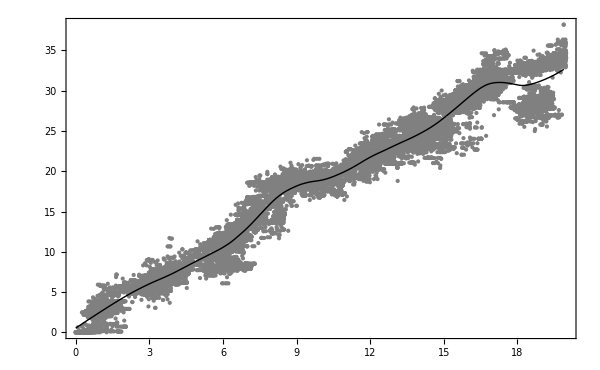

```mathematica
Show[ListPlot[data,PlotStyle->Gray,PlotRange->All],ListLinePlot[loessList,PlotStyle->Directive[Black,Thick]]]
```

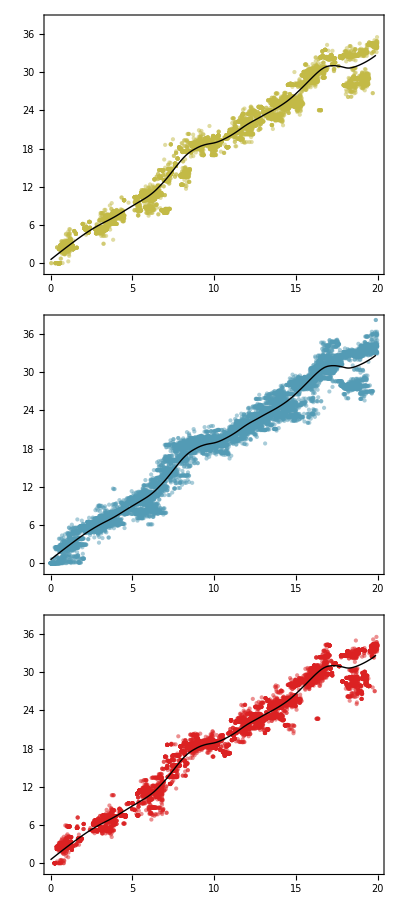

```mathematica
fig=Grid[Table[{Show[ListPlot[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]],PlotStyle->Directive[i/.spatialColorRules,Opacity[0.5]],PlotRange->{-1,max},AspectRatio->0.5],ListLinePlot[loessList,PlotStyle->Directive[Black,Thick]],ImageSize->400]},{i,0,demeCount-1}]]
```

```mathematica
Export["tipsSplineDistance.pdf",fig,"PDF"]
```

tipsSplineDistance.pdf

```mathematica
distance[list_]:=Module[{nf},
nf=Nearest[loessList[[All,1]]->loessList[[All,2]]];
Map[#[[2]]-First[nf[#[[1]]]]&,list]
]
```

```mathematica
Mean[distance[data]]
```

-0.00504388

```mathematica
standardError[list_]:=StandardDeviation[list]/Sqrt[Length[list]]
```

```mathematica
standardError[distance[data]]
```

0.00867649

```mathematica
spatialDists=Table[With[{dist=distance[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]]]},{Mean[dist]-standardError[dist],Mean[dist],Mean[dist]+standardError[dist]}],{i,0,demeCount-1}];
```

```mathematica
TableForm[spatialDists,TableHeadings->{Range[3],{"95% lower","mean","95% upper"}}]
```

| 95% lower | mean | 95% upper
1 | -0.168534 | -0.153893 | -0.139253
2 | 0.0130404 | 0.0290634 | 0.0450863
3 | 0.096309 | 0.110554 | 0.124799

```mathematica
chart=MapIndexed[{GrayLevel[0.3],Line[{{#1[[1]],demeCount-#2[[1]]},{#1[[3]],demeCount-#2[[1]]}}],Line[{{#1[[1]],demeCount-#2[[1]]+0.1},{#1[[1]],demeCount-#2[[1]]-0.1}}],Line[{{#1[[3]],demeCount-#2[[1]]+0.1},{#1[[3]],demeCount-#2[[1]]-0.1}}],PointSize[0.03],spatialColors[[#2[[1]]]],Point[{#1[[2]],demeCount-#2[[1]]}]}&,spatialDists];
```

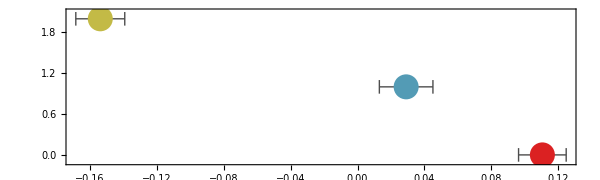

```mathematica
fig=Graphics[chart,AspectRatio->0.3,ImageSize->600,PlotRange->All,Frame->{True,False,True,False},PlotRangePadding->{{0,0},{0.5,0.5}},FrameLabel->{"Distance to AG spline"}]
```

```mathematica
Export["distAGSpatial.pdf",fig,"PDF"]
```

distAGSpatial.pdf

## Trees

First node is child, second is parent

```mathematica
branchScale=0.001;tipScale=0.005;clip=0.005;tipScale=0.001;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;loc=4;layout=5;ag1=6;ag2=7;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{5f8f127c,0.,0,1,0.,0.,0.},{1c88a970,0.,0,0,8.2163,0.,0.},600}

```mathematica
branchData[[1,{1,2},{year,layout}]]
```

{{0.,0.},{0.,8.2163}}

```mathematica
Length[branchData]
```

9170

### Analysis window

```mathematica
branchData=Select[branchData,(#[[1,year]]>clipStartTime&&#[[1,year]]<clipEndTime&&#[[2,year]]>clipStartTime&&#[[2,year]]<clipEndTime&)];
```

### Time vs Layout

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

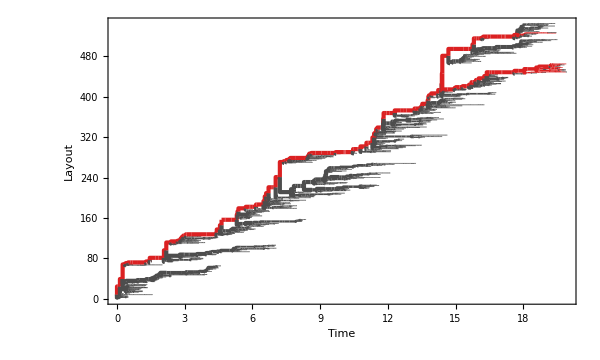

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","Layout"},Frame->{True,True,False,False}]
```

```mathematica
Export["tree.pdf",fig,"PDF"]
```

tree.pdf

### Time vs Distance

```mathematica
clip=0.01
```

0.01

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&)];
```

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{{#[[1,year]],dist[#[[1,{ag1,ag2}]]]},{#[[2,year]],dist[#[[1,{ag1,ag2}]]]},{#[[2,year]],dist[#[[2,{ag1,ag2}]]]}}]}&,trunkBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
list=Map[{#[[1]],dist[#[[{2,3}]]]-RandomReal[{-0.02,0.02}]}&,tipData[[All,{year,ag1,ag2}]]];
```

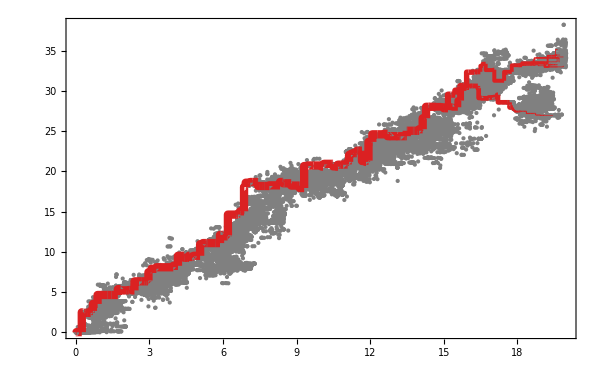

```mathematica
fig=Show[ListPlot[list,PlotStyle->Directive[Gray],PlotRange->All],Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","Antigenic distance"},Frame->{True,True,False,False}]]
```

```mathematica
Export["treeTimeDist.pdf",fig,"PDF"]
```

treeTimeDist.pdf

### Time vs Layout with location

```mathematica
clip=0.005;
```

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

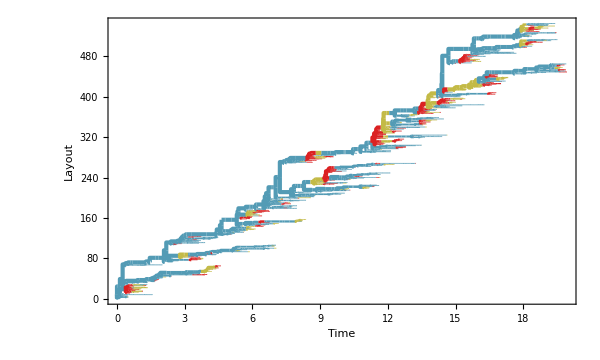

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","Layout"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeSpatial.pdf",fig,"PDF"]
```

treeSpatial.pdf

### AG1 vs AG2

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],Point[#[[1]]]}&,Tally[tipData[[All,{ag1,ag2}]]]];
```

```mathematica
tipPoints={Opacity[0.5],tipPoints};
```

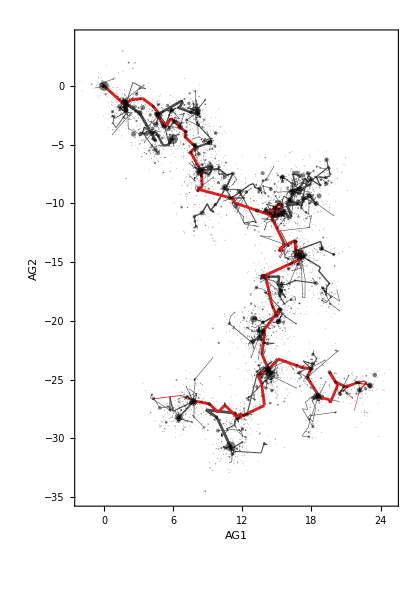

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeAG1AG2.pdf",fig,"PDF"]
```

treeAG1AG2.pdf

### AG1 vs AG2 with location

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],#[[1,3]]/.spatialColorRules,Point[#[[1,{1,2}]]]}&,Tally[tipData[[All,{ag1,ag2,loc}]]]];
```

```mathematica
tipPoints={Opacity[0.5],tipPoints};
```

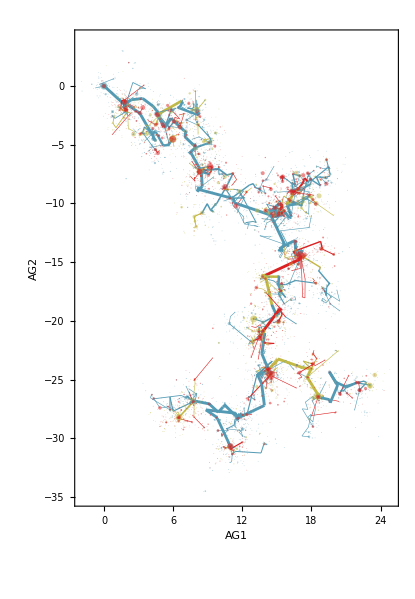

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False}]
```

## Summary statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-1&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-1&)];
```

### Mutation rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0,1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0,1,0]&,sideBranches]];
```

```mathematica
trunkRate=trunkCount/trunkOpportunity
```

4.96268

```mathematica
trunkRate/365
```

0.0135964

```mathematica
sideBranchRate=sideBranchCount/sideBranchOpportunity
```

3.59988

```mathematica
sideBranchRate/365
```

0.00986267

### Antigenic flux

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches]];
```

```mathematica
sideBranchDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches]];
```

```mathematica
trunkRate=trunkDistance/trunkOpportunity
```

3.52445

```mathematica
trunkRate/365
```

0.00965601

```mathematica
sideBranchRate=sideBranchDistance/sideBranchOpportunity
```

1.94711

```mathematica
sideBranchRate/365
```

0.00533454

### Mutation spectrum

```mathematica
trunkMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches],#>0&];
```

```mathematica
sideBranchMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches],#>0&];
```

```mathematica
Length[trunkMutations]
```

122

```mathematica
Mean[sideBranchMutations]
```

0.540882

```mathematica
Mean[trunkMutations]
```

0.71019

```mathematica
comparisonHistogram[list_,col_]:=Show[Histogram[list,{0.25},"PDF",PlotRange->{{0,5},{0,1}},ChartStyle->Directive[EdgeForm[Thin],col],ImageSize->400,Axes->False,Frame->{True,True,False,False}],Plot[PDF[ExponentialDistribution[2],x],{x,0,5},PlotStyle->Directive[Black,Dashed]]];
```

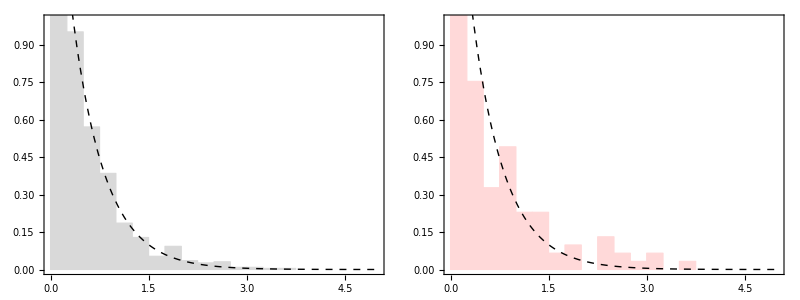

```mathematica
fig=Grid[{{comparisonHistogram[sideBranchMutations,LightGray],comparisonHistogram[trunkMutations,LightRed]}}]
```

### Proportion of each deme in trunk

```mathematica
trunkLengths=Table[Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)]]],{i,0,demeCount-1}];
```

```mathematica
TableForm[trunkLengths/Total[trunkLengths],TableHeadings->{Range[5]}]
```

1 | 0.0718234
2 | 0.880258
3 | 0.047919

### Migration rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,sideBranches]];
```

```mathematica
trunkRate=trunkCount/trunkOpportunity
```

0.52881

```mathematica
(4*trunkRate)/365
```

0.00579518

```mathematica
sideBranchRate=sideBranchCount/sideBranchOpportunity
```

1.00063

```mathematica
(4*sideBranchRate)/365
```

0.0109658

### Migration spectrum

```mathematica
trunkCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkRates=(trunkCounts/trunkOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[trunkRates/.(0.->""),TableHeadings->{Range[demeCount],Range[demeCount]}]
```

| 1 | 2 | 3
1 |  | 2.94846 | 
2 |  |  | 0.19246
3 | 3.53544 |  |

```mathematica
sideBranchCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchRates=(sideBranchCounts/sideBranchOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[sideBranchRates/.(0.->""),TableHeadings->{Range[demeCount],Range[demeCount]}]
```

| 1 | 2 | 3
1 |  | 0.61109 | 0.993021
2 | 0.406065 |  | 0.379867
3 | 0.988581 | 0.329527 |

### Antigenic flux - spatial

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
rate=antigenicDistance/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[rates,TableHeadings->{Range[demeCount]}]
```

1 | 2.20703
2 | 2.1093
3 | 2.11843

### Mutation rate - spatial

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
count=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0,1,0]&,branches]];
rate=count/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[rates,TableHeadings->{Range[demeCount]}]
```

1 | 4.07098
2 | 3.73882
3 | 3.71545

### Mutational spectrum - spatial

All mutations

```mathematica
mutations=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches],#>0&],
{i,0,demeCount-1}];
```

```mathematica
TableForm[Map[Mean,mutations],TableHeadings->{Range[demeCount]}]
```

1 | 0.542137
2 | 0.564161
3 | 0.570168

Trunk mutations

```mathematica
mutations=Table[
branches=Select[branchData,(#[[1,trunk]]==1&&#[[2,trunk]]==1&&#[[1,loc]]==i&&#[[2,loc]]==i&)];
Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches],#>0&],
{i,0,demeCount-1}];
```

```mathematica
mutations
```

{{0.125469,0.345069,2.60411,0.199844,1.28715,0.0502885,2.25713,0.011411,0.75593,0.799058,1.88149,0.0924671},{0.0139176,2.46697,0.222512,0.514273,0.988011,1.15764,0.820649,0.186812,0.0541421,0.047373,1.23762,0.0422167,0.940746,1.07955,0.433566,0.192213,0.462502,1.26116,0.267664,0.309925,0.734109,0.200201,0.116623,1.54319,0.14283,1.40404,0.601586,0.421706,0.209702,2.95028,0.165396,0.39973,3.21515,0.0376524,0.579023,0.160528,0.671974,0.323556,0.420133,1.1558,3.01939,0.709386,0.140663,0.276408,0.128587,0.343582,0.0423249,0.778207,0.0611118,0.698944,1.2644,0.407893,0.33339,0.460992,0.965411,0.141534,0.485875,0.0156822,0.00390512,0.0165239,1.78644,1.43731,0.0746525,0.177676,1.0065,0.278213,1.59347,0.0497362,1.38654,1.1118,0.145542,0.161359,0.920645,0.433885,0.200415,0.319547,0.289588,0.919631,0.682203,0.248675,0.877872,1.76049,0.096537,0.202853,0.3286,1.29818,1.14808,0.706548,0.0939341,0.81268,0.230738,0.83306,1.88355,2.68327,0.505959,0.118412,0.32857,0.0106381,0.767036,1.32835,0.0556141,0.101665,0.0727826,0.118418,0.613363,1.06092,0.994408,0.357798,0.468803,0.21098,0.204174,0.417404,2.37354,0.04608},{0.845519,0.284666,0.342516,3.6682,2.3565,0.0883304,0.613576,0.0567768,0.584981}}

```mathematica
TableForm[Map[Mean,mutations],TableHeadings->{Range[demeCount]}]
```

1 | 0.867451
2 | 0.655983
3 | 0.982341

### Antigenic flux - spatial - absolute

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
antigenicDistance,
{i,0,demeCount-1}];
```

```mathematica
TableForm[rates,TableHeadings->{Range[demeCount]}]
```

1 | 92.1634
2 | 381.373
3 | 114.604